# Zestaw 6

## Zadanie 0. Wyjaśnienie, kiedy `:=`, kiedy `=`

### := (SetDelayed), przypisanie opóźnione

Wykonuje obliczenie w momencie użycia funkcji.
Preferowane kiedy:

wynik zależy od argumentów (x_)

funkcja ma zwracać inny wynik za każdym razem (np. liczby losowe)

gdy używamy zmiennych, które mogą mieć przypisane wartości globalne

Również, kiedy chcemy zrobić wykres funkcji pochodnej tak zdefiniowanej, wtedy najpierw trzeba użyć Evaluate

### = (Set), przypisanie natychmiastowe

Oblicza prawą stronę natychmiast w momencie wciśnięcia Shift+Enter i przypisuje ten wynik do lewej strony.
Preferowane kiedy:

przypisujemy wartości parametrom

gdy obliczenie jest długie (np. całka, skomplikowana pochodna), a wynik się nie zmienia

## Zadanie 1. Całkowanie a parzystość funkcji, Integrate

```mathematica
?Integrate
```

Wykonaj następujące polecenia:

### 1) Oblicz całką nieoznaczoną

gdzie

```mathematica
fn[x_] := x^3 + 4 Sin[5x]
Integrate[fn[x], x]
```

x^4/4-4/5 Cos[5 x]

### 2) Przedstaw funkcję na wykresie

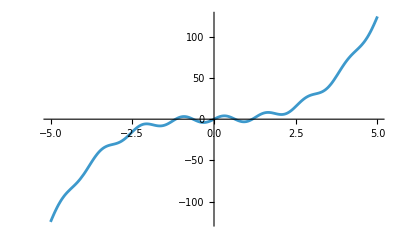

```mathematica
Plot[fn[x], {x, -5, 5}]
```

Oblicz całką oznaczoną z  w zakresie , tj.

```mathematica
Integrate[fn[x], {x, -5, 5}]
```

0

Jaka była wartość całki? Czy można to było wywnioskować bez liczenia całki?
Odp: Tak,  jest funkcją nieparzystą, więc

### 3) Oblicz całką nieoznaczoną

gdzie

```mathematica
fp[x_] := x^2 + 4 Cos[5x]
Integrate[fp[x], x]
```

x^3/3+4/5 Sin[5 x]

### 4) Przedstaw funkcję na wykresie

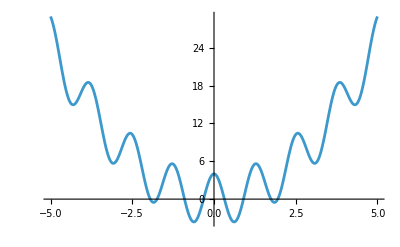

```mathematica
Plot[fp[x], {x, -5, 5}]
```

#### Oblicz całką oznaczoną z w zakresie

Jej wartość oznacz

```mathematica
F[-5, 5] = Integrate[fp[x], {x, -5, 5}]
```

250/3+(8 Sin[25])/5

```mathematica
F[-5, 5]
```

250/3+(8 Sin[25])/5

#### Następnie oblicz wartość całki z w mniejszych przedziałach

tj.  oraz

```mathematica
F[-5, 0] = Integrate[fp[x], {x, -5, 0}]
```

125/3+(4 Sin[25])/5

```mathematica
F[0, 5] = Integrate[fp[x], {x, 0, 5}]
```

125/3+(4 Sin[25])/5

Jaki jest związek między wartościami  a  oraz ? Jak przy całkowaniu zachowują się funkcje parzyste a jak nieparzyste?

```mathematica
F[-5, 0] === F[0, 5]
```

True

```mathematica
F[-5, 5] === F[-5, 0] + F[0, 5]
```

True

## Zadanie 2. Całka a pole pod krzywą, Filling, Show, Graphics, Text, ToString, Style

Oblicz całki oznaczone z funkcji  w zakresie  dla .

```mathematica
f[x_, k_] := 1 / (x^k + 1)

kValues = Range[1, 6];

integrals = Map[
k |-> Integrate[f[x, k], {x, 0, 5}],
kValues
];
```

Następnie:

### 1) Narysuj na osobnych wykresach funkcję

Narysuj na osobnych wykresach funkcję  dla wskazanych wartości  z zaznaczeniem pola pod krzywą.
W tym celu zapoznaj się opcją Filling oraz FillingStyle jeśli chcesz zmienić kolor wypełnienia.
Na wykresach użyj opcji PlotRange -> {All, {0, 1.2}}.

```mathematica
?Filling
```

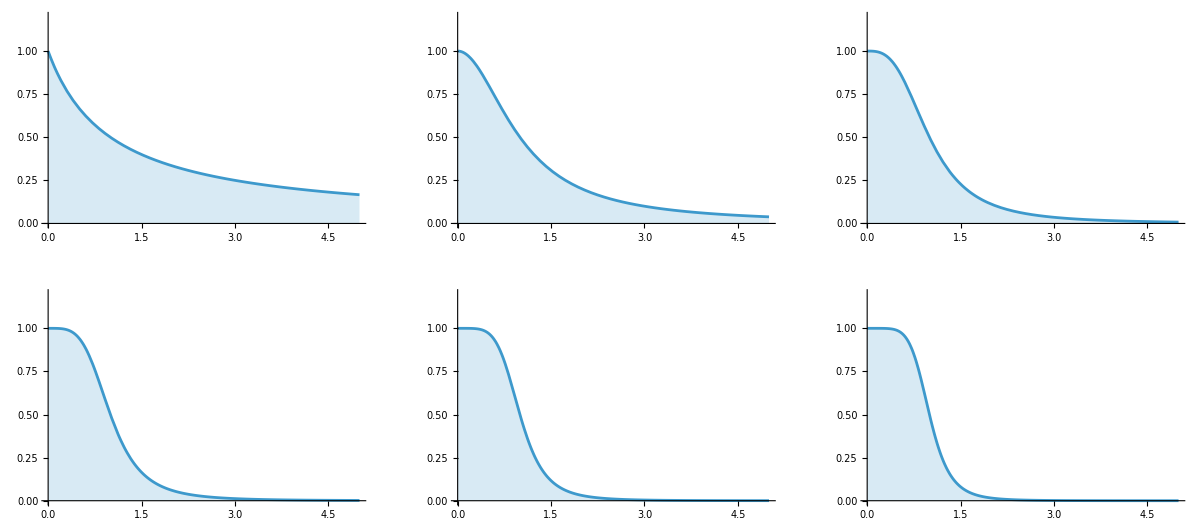

```mathematica
plots = Map[
k |-> Plot[
f[x, k],
{x, 0, 5},
Filling -> Bottom,
PlotRange -> {All, {0, 1.2}}
],
kValues
];

GraphicsGrid @ Partition[plots,3]
```

### 2) Obliczone wartości całek (użyj N) zachowaj w postaci listy poleDo5

```mathematica
poleDo5 = N[integrals]
```

{1.79176,1.3734,1.18926,1.10806,1.06856,1.04713}

Umieść na wykresie informację o obliczonym polu pod krzywą.
Skorzystaj z następującego schematu by nanieść tekst na wykres:

Show[
 	tu_wykres _funkcji,
 	Graphics[ {Text[
    		tu_tekst,
    		tu_współrzędne _tekstu
    	]} ]
 ]

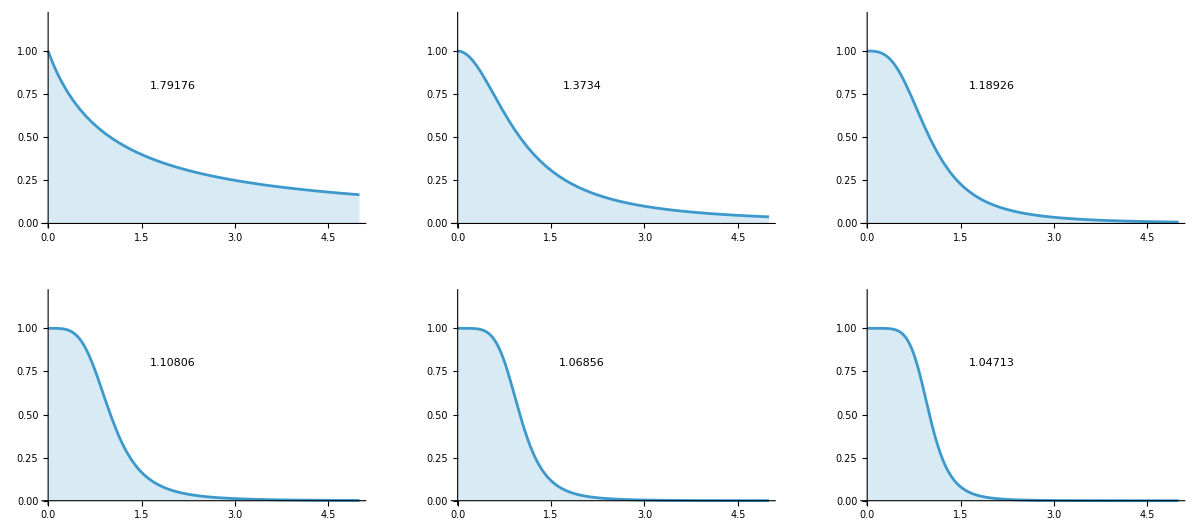

```mathematica
plotsWithValues = Map[
tuple |-> Module[{plot, integralValue},
{plot, integralValue} = tuple;
Show[
plot,
Graphics[ {Text[
integralValue,
{2, 0.8}
]} ]
]
],
Transpose @ {plots, poleDo5}
];

GraphicsGrid @ Partition[plotsWithValues,3]
```

### 3) Następnie policz całki oznaczone dla

Wyniki zapisz jako lista poleDoInf.

```mathematica
poleDoInf =  Map[
k |-> Integrate[f[x, k], {x, 0, Infinity}],
kValues
]
```

Integrate::idiv: Integral of 1/(1+x) does not converge on {0,∞}.

{∫_0^∞ 1/(1+x)ⅆx,π/2,(2 π)/(3 √3),π/(2 √2),1/5 Gamma[1/5] Gamma[4/5],π/3}

```mathematica
poleDoInf = Join[{Infinity}, N @ poleDoInf[[2;;]]]
```

{∞,1.5708,1.2092,1.11072,1.06896,1.0472}

### 4) Porównaj wartości list poleDo5 oraz poleDoInf

Jaki jest stosunek pola pod krzywą dla całki liczonej do  do pola dla całki liczonej do  przy rosnącym ?
Ile wynosi ten stosunek dla .
Co dzieje się przy ?

```mathematica
Map[
tuple |-> Module[{k, integralTo5, integralToInf},
{k, integralTo5, integralToInf} = tuple;
k  -> PercentForm[integralTo5 / integralToInf]
],
Transpose @ {kValues, poleDo5, poleDoInf}
]
```

{1→0%,2→87.43%,3→98.35%,4→99.76%,5→99.96%,6→99.99%}

## Zadanie 3. Pole pomiędzy krzywymi, RegionPlot, ImplicitRegion, Area

Obliczyć pole obszaru ograniczonego od dołu krzywą  a od góry krzywą .

```mathematica
b[x_] := x^2
t[x_] := 2 / (x^2 + 1)
```

W tym celu:

### 1) Zaznaczyć interesujący obszar na wspólnym wykresie obu funkcji (krzywych)

Można użyć kombinacji funkcji Show, Plot, oraz RegionPlot.

```mathematica
?RegionPlot
```

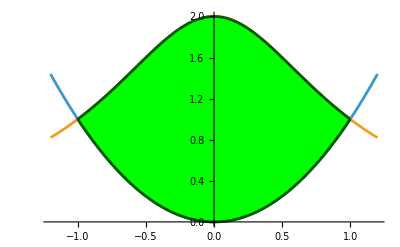

```mathematica
solutions = Map[
solution |-> Last[solution],
Flatten @ Solve[b[x] == t[x], x, Reals]
];

{xMin, xMax} = solutions;
xRange ={x, xMin, xMax};
{yMin, yMax} = {MinValue[b[x], x], MaxValue[t[x], x]};

Show[
Plot[
{b[x], t[x]},
Join[{x}, 1.2 * solutions]
],
RegionPlot[
b[x] <= y <= t[x], 
xRange,{y, yMin, yMax} ,
PlotStyle -> Green, BoundaryStyle->DarkGreen]
]
```

### 2) Odczytać z wykresu lub znaleźć przy pomocy Solve miejsca przecięcia obu krzywych

```mathematica
solutions = Map[
solution |-> Last[solution],
Flatten @ Solve[b[x] == t[x], x, Reals]
]
```

{-1,1}

### 3) Użyć wyznaczonego w 2) zakresu wartości do obliczenia pola powierzchni między tymi krzywymi

Użyć wyznaczonego w 2) zakresu wartości  do obliczenia pola powierzchni między tymi krzywymi jako całki oznaczonej z  . Zapisać wynik.

```mathematica
areaIntegral = Integrate[t[x] - b[x], xRange]
```

-2/3+π

### 4) Wynik z 3) można uzyskać również inaczej za pomocą wbudowanych funkcji określających obszar (region) geometryczny

W tym celu zdefiniować interesujący nas region korzystając z ImplicitRegion a następnie wyznaczyć pole korzystając z funkcji Area.

```mathematica
?ImplicitRegion
```

```mathematica
region = ImplicitRegion[b[x] <= y <= t[x], {{x, xMin, xMax}, {y,yMin, yMax}}]
```

ImplicitRegion[x^2≤y≤2/(1+x^2)&&-1≤x≤1&&0≤y≤2,{x,y}]

```mathematica
?Area
```

```mathematica
areaBuildInFunction = Area[region]
```

-2/3+π

Porównać z wynikiem z 3)

```mathematica
areaIntegral === areaBuildInFunction
```

True

## Zadanie 4. Długość łuku, Integrate, NIntegrate, ArcLength

Oblicz długość łuku zadanego przez krzywą  dla  .12.

```mathematica
f[x_] := x^3 + 1/x^3
xRange = {x, 0.5, 2};
```

W tym celu:

#### 1) Narysuj wykres zadanej krzywej (w celach poglądowych)

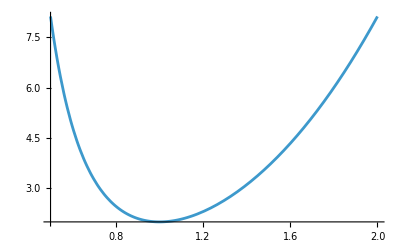

```mathematica
Plot[f[x], xRange]
```

### 2) Skorzystaj ze wzoru na długość łuku krzywej

, gdzie ,  to krańce zakresu całkowania.

```mathematica
xRange
```

{x,0.5,2}

```mathematica
Integrate[
Sqrt[1 + f'[x]^2],
xRange
]
```

∫_0.5^2 √(1+(-3/x^4+3 x^2)^2)ⅆx

Czy tę całkę da się wyrazić analitycznie? Użyj N albo NIntegrate.

```mathematica
lengthFromDefinition = NIntegrate[
Sqrt[1 + f'[x]^2],
xRange
]
```

12.4611

### 3) Policz długość łuku krzywej korzystając z funkcji ArcLength

```mathematica
?ArcLength
```

Można bezpośrednio lub definiując łuk jako region korzystając z ImplicitRegion.
Porównaj wyniki z 2).

```mathematica
lengthBuildInFunction = ArcLength[f[x], xRange]
```

12.4611

```mathematica
lengthBuildInFunction == lengthFromDefinition
```

True

## Zadanie 5. Środek ciężkości łuku krzywej, Integrate, NIntegrate, RegionCentroid, ImplicitRegion

Wyznaczyć środek masy  dla jednorodnego łuku zadanego przez krzywą z poprzedniego zadania, tj. dla  .12.
W tym celu:

### 1) Skorzystaj ze wzoru na oraz

oraz 
gdzie ,  to krańce zakresu całkowania,  długość łuku, a .

```mathematica
l = lengthBuildInFunction;

xCm = 1/l * NIntegrate[
x Sqrt[ 1 + f'[x]^2 ],
xRange
]
```

1.13659

```mathematica
yCm = 1/l * NIntegrate[
f[x] Sqrt[ 1 + f'[x]^2 ],
xRange
]
```

5.02299

### 2) Przedstawić punkt na wykresie razem z krzywą zadaną przez

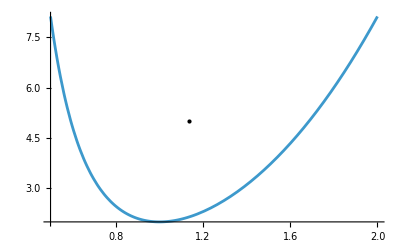

```mathematica
Plot[
f[x],
xRange,
Epilog->{
PointSize[Large],Point[{xCm, yCm}]
}
]
```

### 3) Wyznaczyć środek ciężkości korzystając z funkcji RegionCentroid

W tym celu najpierw zdefiniować łuk krzywej jako region z użyciem funkcji ImplicitRegion.

```mathematica
massCenterPoint = RegionCentroid[
ImplicitRegion[y == f[x] && 0.5 <= x <= 2, {x, y}]
]
```

{1.13661,5.02388}

Porównać wynik z 1).

```mathematica
"Integral:          " <> ToString @ {xCm, yCm}
"Build-in function: " <> ToString @ massCenterPoint
```

Integral:          {1.13659, 5.02299}

Build-in function: {1.13661, 5.02388}